```mathematica
SystemOptions["ParallelOptions"->"MKLThreadNumber"]
{"ParallelOptions"->{"MKLThreadNumber"->2}}
sigmax=N[{{0,1},{1,0}}];
sigmay=N[{{0,-I},{I,0}}];
sigmaz=N[{{1,0},{0,-1}}];
sigma={sigmax,sigmay,sigmaz};
spinclouping[s_,j_,i_,k_]:=ReplacePart[s,{j-> N[sigma[[k]].s[[j]]],i-> N[sigma[[k]].s[[i]]]}]
Jx=Compile[{{θ,_Real}}, Cos[θ]-0.5*Sin[θ],CompilationTarget->"C",Parallelization->True]
Jz= Compile[{{θ,_Real}}, 0.5*Sin[θ],CompilationTarget->"C",Parallelization->True]
r[n_,m_]:=Table[N[{Mod[j-1,n]+0.5*Floor[(j-1)/n],Sin[Pi/3]*(Floor[j/(n+1)])}],{j,n*m}]
eigenvalue[vec_,mat_]:=N[Re[Conjugate[vec].(mat.vec)/Sqrt[Conjugate[vec].vec]]]

samestate=Function[{a,b} ,Module[{result=1,i},
For[i=1,i≤ Length[a],i++,
If[a[[i]][[1]]≠ b[[i]][[1]] ||  a[[i]][[2]]≠ b[[i]][[2]],
result=0];
];
result
]];

indep=N[{{1,5,9},{3,4,8},{2,6,7}}];
indep8={{5,6},{5,6},{7,8},{7,8},{1,2},{1,2},{3,4},{3,4}};
indep6={{5},{6},{4},{3},{1},{2}};
neighbors[j_,k_]:=For[indice=1,indice≤ 3,indice++ , If[MemberQ[indep[[indice]],j],If[MemberQ[indep[[indice]],k], Return[0], Return[1]]]]
neighbors8[j_,k_]:=If[MemberQ[indep8[[j]],k],Return[0],Return[1]]
neighbors6[j_,k_]:=If[MemberQ[indep6[[j]],k],Return[0],Return[1]]

Hxxz[θ_,s_,N_]:= Sum[neighbors6[j,k]*(Jx[θ]*(spinclouping[s,j,k,1]+spinclouping[s,j,k,2])+Jz[θ]*spinclouping[s,j,k,3]),{j,1,N},{k,1,N}]
Hxxz1D[θ_,s_,N_,pb_]:= Sum[Jx[θ]*(spinclouping[s,j,j+1,1]+spinclouping[s,j,j+1,2])+Jz[θ]*spinclouping[s,j,j+1,3],{j,1,N-1}]+pb*(Jx[θ]*(spinclouping[s,N,1,1]+spinclouping[s,N,1,2])+Jz[θ]*spinclouping[s,N,1,3])
```

{ParallelOptions→{MKLThreadNumber→2}}

{ParallelOptions→{MKLThreadNumber→2}}

CompiledFunction[…]

CompiledFunction[…]

```mathematica
Nsites=6;
points=50;
pb=1;
θ=N[Range[-Pi,Pi,2*Pi/points]];
k=Pi;
s0=1;
Sav={};
EE={};
pos=r[3,2];
system=Range[Nsites];
regionB={{6},{5,6},{3,5,6},{2,3,5,6},{2,3,4,5,6}};
npartitions=Length[regionB]
regionA=Table[Delete[system,Partition[regionB[[j]],1]],{j,npartitions}]
Nb=Table[Length[regionB[[j]]],{j,npartitions}]
Na=Table[Length[regionA[[j]]],{j,npartitions}]
EEmax=Table[N[Min[Na[[j]],Nb[[j]]]*Log[2]],{j,npartitions}]
ssystem=N[Tuples[{{1,0},{0,1}},Nsites]];
sHilbert=N[ssystem/Sqrt[Nsites]];
sA=Table[N[Tuples[{{1,0},{0,1}},Na[[j]]]],{j,npartitions}];

traceset=Function[{j1,j2,p},Module[{list={},a1,a2,b1,b2,i,k},
For[i=1,i≤ 2^ Nsites,i++,
For[k=1,k≤ 2^Nsites,k++,
b1=Delete[ssystem[[i]],Partition[regionA[[p]],1]];
b2=Delete[ssystem[[k]],Partition[regionA[[p]],1]];
a1=Delete[ssystem[[i]],Partition[regionB[[p]],1]];
a2=Delete[ssystem[[k]],Partition[regionB[[p]],1]];
If[samestate[a1,sA[[p]][[j1]]]== 1&& samestate[a2,sA[[p]][[j2]]]== 1 && samestate[b1,b2]== 1,
list=AppendTo[list,{i,k}];
];
];
];
list
]
];
tracedone=ParallelTable[Table[traceset[j1,j2,p],{j1,2^Na[[p]]},{j2,2^Na[[p]]}],{p,npartitions}];
```

5

{{1,2,3,4,5},{1,2,3,4},{1,2,4},{1,4},{1}}

{1,2,3,4,5}

{5,4,3,2,1}

{0.693147,1.38629,2.07944,1.38629,0.693147}

EE[1][1]=0.000107207

EE[2][1]=0.0000826835

EE[3][1]=0.0000614334

EE[4][1]=0.0000826835

EE[5][1]=0.000107207

EE[1][2]=0.0000985089

EE[2][2]=0.0000759948

EE[3][2]=0.0000564676

EE[4][2]=0.0000759948

EE[5][2]=0.0000985089

EE[1][3]=0.000091264

EE[2][3]=0.000070422

EE[3][3]=0.0000523298

EE[4][3]=0.000070422

EE[5][3]=0.000091264

EE[1][4]=0.0000858721

EE[2][4]=0.0000662735

EE[3][4]=0.0000492495

EE[4][4]=0.0000662735

EE[5][4]=0.0000858721

EE[1][5]=0.0000834563

EE[2][5]=0.0000644145

EE[3][5]=0.0000478691

EE[4][5]=0.0000644145

EE[5][5]=0.0000834563

EE[1][6]=0.000087014

EE[2][6]=0.0000671522

EE[3][6]=0.0000499019

EE[4][6]=0.0000671522

EE[5][6]=0.000087014

EE[1][7]=0.000105772

EE[2][7]=0.0000815801

EE[3][7]=0.0000606142

EE[4][7]=0.0000815801

EE[5][7]=0.000105772

EE[1][8]=0.000177547

EE[2][8]=0.000136711

EE[3][8]=0.000101532

EE[4][8]=0.000136711

EE[5][8]=0.000177547

EE[1][9]=0.000550609

EE[2][9]=0.000422166

EE[3][9]=0.000313181

EE[4][9]=0.000422166

EE[5][9]=0.000550609

EE[1][10]=0.00484793

EE[2][10]=0.00367374

EE[3][10]=0.00271688

EE[4][10]=0.00367374

EE[5][10]=0.00484793

EE[1][11]=0.157382

EE[2][11]=0.114581

EE[3][11]=0.0838382

EE[4][11]=0.114581

EE[5][11]=0.157382

EE[1][12]=0.544247

EE[2][12]=0.386082

EE[3][12]=0.280596

EE[4][12]=0.386082

EE[5][12]=0.544247

EE[1][13]=0.877722

EE[2][13]=0.864673

EE[3][13]=0.672477

EE[4][13]=0.836863

EE[5][13]=0.87884

EE[1][14]=0.903043

EE[2][14]=0.858884

EE[3][14]=0.709026

EE[4][14]=0.835294

EE[5][14]=0.986715

EE[1][15]=0.903939

EE[2][15]=0.801722

EE[3][15]=0.642847

EE[4][15]=0.73539

EE[5][15]=0.855325

EE[1][16]=0.250286

EE[2][16]=0.175686

EE[3][16]=0.127157

EE[4][16]=0.175686

EE[5][16]=0.250286

EE[1][17]=0.945993

EE[2][17]=0.747185

EE[3][17]=0.585547

EE[4][17]=0.784064

EE[5][17]=0.777613

EE[1][18]=0.972916

EE[2][18]=0.889269

EE[3][18]=0.637949

EE[4][18]=0.833959

EE[5][18]=0.881268

EE[1][19]=0.820636

EE[2][19]=0.77516

EE[3][19]=0.699484

EE[4][19]=0.913559

EE[5][19]=0.969787

EE[1][20]=0.969258

EE[2][20]=0.823192

EE[3][20]=0.722518

EE[4][20]=0.925221

EE[5][20]=0.978405

EE[1][21]=0.675726

EE[2][21]=0.621616

EE[3][21]=0.462897

EE[4][21]=0.574594

EE[5][21]=0.723541

EE[1][22]=0.568866

EE[2][22]=0.463601

EE[3][22]=0.425715

EE[4][22]=0.474459

EE[5][22]=0.513689

EE[1][23]=0.694659

EE[2][23]=0.725216

EE[3][23]=0.538155

EE[4][23]=0.641738

EE[5][23]=0.581485

EE[1][24]=0.770397

EE[2][24]=0.848771

EE[3][24]=0.654277

EE[4][24]=0.804202

EE[5][24]=0.80313

EE[1][25]=0.64279

EE[2][25]=0.641767

EE[3][25]=0.506459

EE[4][25]=0.719577

EE[5][25]=0.753451

EE[1][26]=0.799802

EE[2][26]=0.717019

EE[3][26]=0.571368

EE[4][26]=0.660513

EE[5][26]=0.748183

EE[1][27]=0.914887

EE[2][27]=0.850286

EE[3][27]=0.672003

EE[4][27]=0.87176

EE[5][27]=0.962669

EE[1][28]=0.773599

EE[2][28]=0.819954

EE[3][28]=0.672314

EE[4][28]=0.856428

EE[5][28]=0.958341

EE[1][29]=0.712663

EE[2][29]=0.72243

EE[3][29]=0.566

EE[4][29]=0.76007

EE[5][29]=0.773531

EE[1][30]=0.93281

EE[2][30]=0.879071

EE[3][30]=0.702922

EE[4][30]=0.928985

EE[5][30]=0.926882

EE[1][31]=0.974314

EE[2][31]=0.874335

EE[3][31]=0.692563

EE[4][31]=0.857873

EE[5][31]=0.887843

EE[1][32]=0.957585

EE[2][32]=0.885531

EE[3][32]=0.707153

EE[4][32]=0.870823

EE[5][32]=0.955183

EE[1][33]=0.972788

EE[2][33]=0.93331

EE[3][33]=0.815607

EE[4][33]=0.940369

EE[5][33]=0.964172

EE[1][34]=0.872055

EE[2][34]=0.886548

EE[3][34]=0.711039

EE[4][34]=0.875017

EE[5][34]=0.995071

EE[1][35]=0.981635

EE[2][35]=0.832477

EE[3][35]=0.695739

EE[4][35]=0.859885

EE[5][35]=0.977655

EE[1][36]=0.297104

EE[2][36]=0.213642

EE[3][36]=0.155814

EE[4][36]=0.213642

EE[5][36]=0.297104

EE[1][37]=0.0184631

EE[2][37]=0.0138377

EE[3][37]=0.0102034

EE[4][37]=0.0138377

EE[5][37]=0.0184631

EE[1][38]=0.00329795

EE[2][38]=0.0025055

EE[3][38]=0.00185417

EE[4][38]=0.0025055

EE[5][38]=0.00329795

EE[1][39]=0.00128889

EE[2][39]=0.000984365

EE[3][39]=0.00072949

EE[4][39]=0.000984365

EE[5][39]=0.00128889

EE[1][40]=0.000718876

EE[2][40]=0.000550546

EE[3][40]=0.000408295

EE[4][40]=0.000550546

EE[5][40]=0.000718876

EE[1][41]=0.000482335

EE[2][41]=0.000370021

EE[3][41]=0.000274538

EE[4][41]=0.000370021

EE[5][41]=0.000482335

EE[1][42]=0.000359986

EE[2][42]=0.000276483

EE[3][42]=0.0002052

EE[4][42]=0.000276483

EE[5][42]=0.000359986

EE[1][43]=0.000287006

EE[2][43]=0.00022062

EE[3][43]=0.000163776

EE[4][43]=0.00022062

EE[5][43]=0.000287006

EE[1][44]=0.000238912

EE[2][44]=0.000183773

EE[3][44]=0.000136447

EE[4][44]=0.000183773

EE[5][44]=0.000238912

EE[1][45]=0.000204795

EE[2][45]=0.000157615

EE[3][45]=0.000117042

EE[4][45]=0.000157615

EE[5][45]=0.000204795

EE[1][46]=0.000179181

EE[2][46]=0.000137965

EE[3][46]=0.000102462

EE[4][46]=0.000137965

EE[5][46]=0.000179181

EE[1][47]=0.00015907

EE[2][47]=0.000122529

EE[3][47]=0.000091008

EE[4][47]=0.000122529

EE[5][47]=0.00015907

EE[1][48]=0.000142706

EE[2][48]=0.000109963

EE[3][48]=0.0000816822

EE[4][48]=0.000109963

EE[5][48]=0.000142706

EE[1][49]=0.00012901

EE[2][49]=0.0000994418

EE[3][49]=0.0000738735

EE[4][49]=0.0000994418

EE[5][49]=0.00012901

EE[1][50]=0.000117312

EE[2][50]=0.0000904516

EE[3][50]=0.0000672001

EE[4][50]=0.0000904516

EE[5][50]=0.000117312

EE[1][51]=0.000107207

EE[2][51]=0.0000826835

EE[3][51]=0.0000614334

EE[4][51]=0.0000826835

EE[5][51]=0.000107207

Part::partw: Part 6 of {0.0000743101,0.000114624,0.000127747,0.000114624,0.0000743101} does not exist.

Part::partw: Part 7 of {0.0000743101,0.000114624,0.000127747,0.000114624,0.0000743101} does not exist.

Part::partw: Part 8 of {0.0000743101,0.000114624,0.000127747,0.000114624,0.0000743101} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Table::iterb: Iterator {PlotLegends→Expressions} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table::iterb: Iterator {PlotLegends→Expressions} does not have appropriate bounds.

Show::gcomb: Could not combine the graphics objects in Show[Table[Plot[fEE⟦p⟧[x],{x,-1,1}],{p,5},{PlotLegends→Expressions}],].

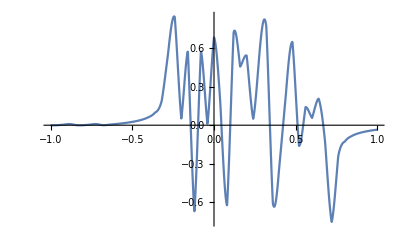
Show[Table[Plot[fEE⟦p⟧[x],{x,-1,1}],{p,5},{PlotLegends→Expressions}],-Graphics-]

```mathematica
Clear[EE];
EE={};
For[p=1,p≤ Length[θ],p++,
m= ParallelTable[N[Sum[Conjugate[sHilbert[[j]]][[k]].Hxxz[θ[[p]],sHilbert[[i]],Nsites][[k]],{k,Nsites}]],{i,2^Nsites},{j,2^Nsites}];
basis=N[ Eigenvectors[m]];
gs=basis[[1]];
For[i=2,i≤ 2^Nsites,i++, If[eigenvalue[gs,m]>eigenvalue[basis[[i]],m],gs=basis[[i]]]]
Clear[i];
gs=gs/Sqrt[Conjugate[gs].gs];
ground= ParallelSum[gs[[i]]*sHilbert[[i]],{i,2^Nsites}];
norm = ParallelTable[ground[[i]]/Sqrt[Conjugate[ground[[i]]].ground[[i]]],{i,Nsites}];
AppendTo[Sav,N[ParallelSum[Abs[norm[[n]][[1]]]^2-Abs[norm[[n]][[2]]]^ 2,{n,Nsites}]]/Nsites];
EEp={};
For[h=1,h≤ npartitions,h++,
ρ=ParallelTable[
Sum[Conjugate[gs[[tracedone[[h]][[j]][[l]][[n]][[1]]]]]*gs[[tracedone[[h]][[j]][[l]][[n]][[2]]]],
{n,Length[tracedone[[h]][[j]][[l]]]}],
{j,2^Na[[h]]},{l,2^Na[[h]]}];
lambda=N[Eigenvalues[ρ]];
AppendTo[EEp,N[Re[-Sum[lambda[[i]]*Log[lambda[[i]]],{i,Length[lambda]}]]]];
Print["EE[",h,"][",p,"]=",EEp[[h]]/EEmax[[h]]]
]
AppendTo[EE,EEp];
]
dataSav=Table[{θ[[j]]/Pi,Sav[[j]]},{j,Length[θ]}];
dataEE=Table[Table[{θ[[j]]/Pi,EE[[p]][[j]]/EEmax},{j,Length[θ]}],{p,npartitions}];
fEE=Table[Interpolation[dataEE[[p]]],{p,npartitions}];
fSav=Interpolation[dataSav];
plotEE=Table[Plot[fEE[[p]][x],{x,-1,1}],{p,npartitions},PlotLegends->"Expressions"];
plotSav=Plot[fSav[x],{x,-1,1},PlotLegends->"Expressions"];
Show[plotEE,plotSav]
```

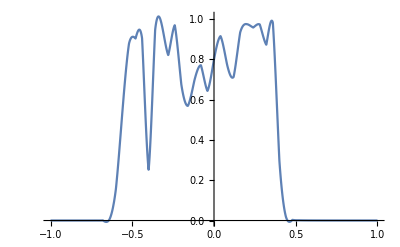
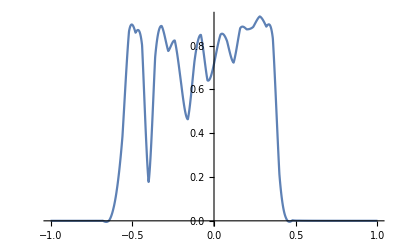
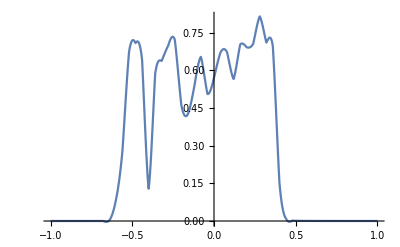
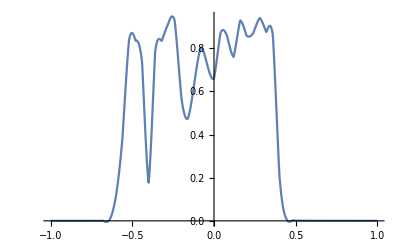
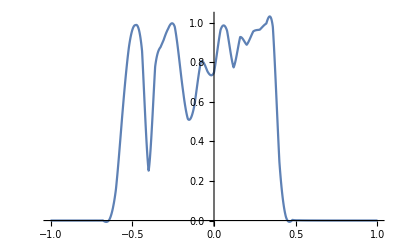

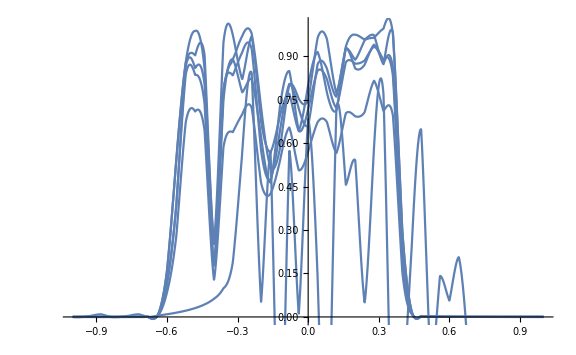

```mathematica
dataSav=Table[{θ[[j]]/Pi,Sav[[j]]},{j,Length[θ]}];
dataEE=Table[Table[{θ[[j]]/Pi,EE[[j]][[p]]/EEmax[[p]]},{j,Length[θ]}],{p,npartitions}];
fEE=Table[Interpolation[dataEE[[p]]],{p,npartitions}];
EntEnt[x_]=Table[fEE[[p]][x],{p,npartitions}];
fSav=Interpolation[dataSav];
plotEE=Table[Plot[fEE[[p]][x],{x,-1,1},PlotLegends-> "test"],{p,npartitions}]
plotSav=Plot[fSav[x],{x,-1,1},PlotLegends->"Expressions"];
Show[AppendTo[plotEE,plotSav],ImageSize-> Large]
```

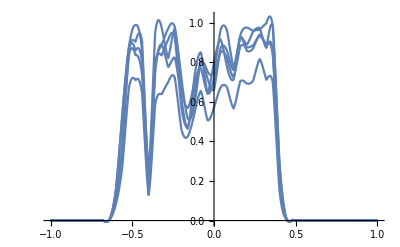

```mathematica
Plot[Table[EntEnt[x][[p]],{p,npartitions}],{x,-1,1}]
```

```mathematica
fEE[[1]][0]
```

0.799802

```mathematica
Plot[fEE[x],{x,-1,1},PlotLegends->"Expressions"]
```

-Graphics-

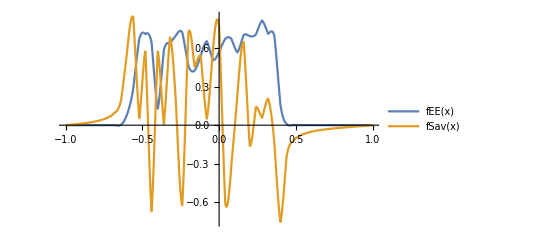

```mathematica
Plot[{fEE[x],fSav[x]},{x,-1,1},PlotLegends->"Expressions"]
```

```mathematica
Max[EE]
```

1.16925

```mathematica
S= N[Re[ParallelSum[Exp[I*k*EuclideanDistance[pos[[j]],pos[[s0]]]]*Sum[Conjugate[norm[[n]]].spinclouping[norm,j,s0,r][[n]],{n,Nsites},{r,3}],{j,Nsites}]]]
```

```mathematica
Clear[Sav,EE]
```